Let’s first input the geometric data from sage to build an effective field theory: First input the volume:

```mathematica
filename ="/Users/cody/Dropbox/KSGeometryAnalysis/SmallSampleAnalysis/h11-15.txt";
dataall =ToExpression[StringReplace[ToString[Import[filename]],{"'" -> "","N" -> "II"}]];
```

```mathematica
Length[dataall]
```

200

```mathematica
allevals = {};
For[fn =1,fn≤Length[dataall],fn++,{
data = dataall[[fn]][[1]];
J = data[[1]];
vol = data[[3]][[1]];
mori = data[[4]];
τ = D[vol,{J,1}];
A = D[τ,{J,1}];
Kinv = 4(-vol*D[vol,{J,2}] + Outer[Times,τ,τ]);
pt = FindInstance[Table[mori[[mm]]≥1.,{mm,1,Length[mori]}],J][[1]];
vnum = vol/.pt;
jnum = J/.pt;
pt2 = Table[J[[ii]]->jnum[[ii]]/vnum^(1/3),{ii,1,Length[J]}];
Kinvnum = Kinv/.pt2;
evals = Kinvnum//Eigenvalues;
AppendTo[allevals,evals];
}];
```

```mathematica
Length[Flatten[allevals]]
```

3000

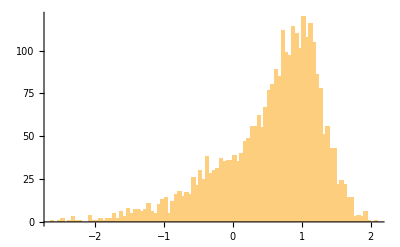

```mathematica
Histogram[Log10[Flatten[allevals]],100]
```

```mathematica
Max[Flatten[allevals]]
```

120.367

```mathematica
Min[Flatten[allevals]]
```

0.00239721

```mathematica
Mean[Flatten[allevals]]
```

8.63804

```mathematica
CentralMoment[Flatten[allevals],2]
```

116.037

```mathematica
CentralMoment[Flatten[allevals],3]
```

3799.32

```mathematica
5^6
```

15625

```mathematica
vol/.pt2
```

1.